# SemiEulerianGraphQ

test if a connected undirected graph is semi Eulerian

## Definition

```mathematica
ClearAll[SemiEulerianGraphQ]
SemiEulerianGraphQ[graph_?(ConnectedGraphQ[#]∧UndirectedGraphQ[#]&)]:=Count[VertexDegree[graph],x_/;OddQ[x]]<=2
```

## Documentation

### Usage

SemiEulerianGraphQ[arg]

explanation of what use of the argument arg does.

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

Text about the example:

```mathematica
MyFunction[x,y]
```

x y

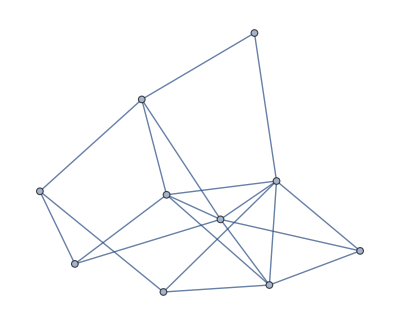

```mathematica
RandomGraph[{10,20}]
```

```mathematica
VertexDegree[RandomGraph[{6,15}]]
```

{5,5,5,5,5,5}

```mathematica
VertexDegree[RandomGraph[{7,19}]]
```

{5,5,5,5,6,6,6}

```mathematica
VertexDegree[RandomGraph[{7,20}]]
```

{6,6,6,5,6,5,6}

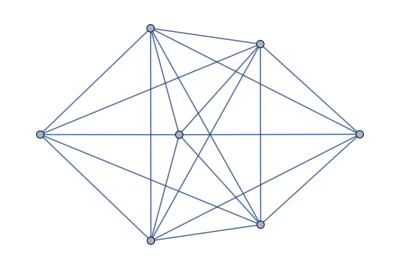

```mathematica
RandomGraph[{7,20}]
```

```mathematica
SemiEulerianGraphQ[RandomGraph[{7,20}]]
```

True

```mathematica
EulerianGraphQ[RandomGraph[{7,20}]]
```

False

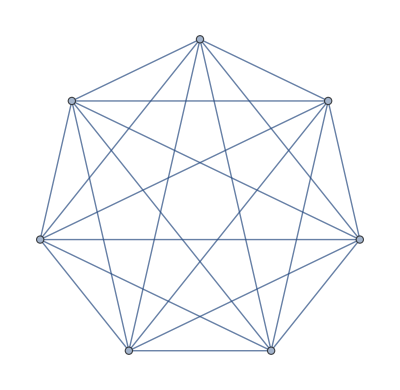

```mathematica
RandomGraph[{7,21}]
```

```mathematica
VertexDegree[RandomGraph[{7,21}]]
```

{6,6,6,6,6,6,6}

```mathematica
SemiEulerianGraphQ[RandomGraph[{7,21}]]
```

True

```mathematica
EulerianGraphQ[RandomGraph[{7,21}]]
```

True

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Author Name

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.